## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=2.0;
```

```mathematica
winit=(0.3-0.00005*I)
```

0.3-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+10^(-3);r1=30 ;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.277505+0.0000853694 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=M+10^(-3);r1=30; wc=qscal;
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-2*I*M*(wres-wc);
sigmasol=M*(qscal*wres+mu^2-2*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[
{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (wres*r^2-qscal*M*r)^2/(r-M)^4 - 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(wres-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

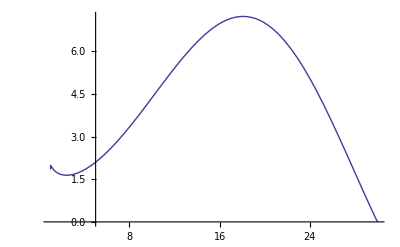

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,r0,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.3-0.00005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 +ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);

sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.3-0.00005*I);
ie=0;While[ie<51,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,50}]
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,50}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{30.,0.277505},{29.8,0.278925},{29.6,0.280364},{29.4,0.281824},{29.2,0.283305},{29.,0.284806},{28.8,0.286329},{28.6,0.287874},{28.4,0.289441},{28.2,0.291031},{28.,0.292644},{27.8,0.29428},{27.6,0.295941},{27.4,0.297627},{27.2,0.299338},{27.,0.301074},{26.8,0.302837},{26.6,0.304627},{26.4,0.306445},{26.2,0.30829},{26.,0.310164},{25.8,0.312068},{25.6,0.314001},{25.4,0.315966},{25.2,0.317961},{25.,0.319989},{24.8,0.32205},{24.6,0.324144},{24.4,0.326273},{24.2,0.328437},{24.,0.330637},{23.8,0.332874},{23.6,0.335148},{23.4,0.337462},{23.2,0.339815},{23.,0.342208},{22.8,0.344643},{22.6,0.347122},{22.4,0.349643},{22.2,0.35221},{22.,0.354823},{21.8,0.357482},{21.6,0.360191},{21.4,0.362949},{21.2,0.365758},{21.,0.368619},{20.8,0.371535},{20.6,0.374505},{20.4,0.377533},{20.2,0.380618},{20.,0.383764}}

```mathematica
winit=(0.35-0.00005*I);
ie=0;While[ie<25,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=20 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l2=Table[{N[radit[n],10],Re[witer[n]]},{n,0,24}]
t2l2=Table[{N[radit[n],10],Im[witer[n]]},{n,0,24}];
```

{{20.,0.383764},{19.8,0.386971},{19.6,0.390242},{19.4,0.393578},{19.2,0.396981},{19.,0.400453},{18.8,0.403996},{18.6,0.407613},{18.4,0.411304},{18.2,0.415074},{18.,0.418923},{17.8,0.422855},{17.6,0.426872},{17.4,0.430977},{17.2,0.435172},{17.,0.439461},{16.8,0.443846},{16.6,0.448331},{16.4,0.452919},{16.2,0.457613},{16.,0.462417},{15.8,0.467335},{15.6,0.472371},{15.4,0.477528},{15.2,0.482811}}

```mathematica
winit=(0.5-0.00005*I);
ie=0;While[ie<26,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=15 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l3=Table[{N[radit[n],10],Re[witer[n]]},{n,0,25}]
t2l3=Table[{N[radit[n],10],Im[witer[n]]},{n,0,25}];
```

{{15.,0.488225},{14.8,0.493774},{14.6,0.499463},{14.4,0.505298},{14.2,0.511283},{14.,0.517425},{13.8,0.523729},{13.6,0.530202},{13.4,0.53685},{13.2,0.543681},{13.,0.550701},{12.8,0.557919},{12.6,0.565342},{12.4,0.57298},{12.2,0.58084},{12.,0.588933},{11.8,0.597269},{11.6,0.605858},{11.4,0.614712},{11.2,0.623843},{11.,0.633263},{10.8,0.642985},{10.6,0.653025},{10.4,0.663397},{10.2,0.674118},{10.,0.685204}}

```mathematica
winit=(0.70-0.00005*I);
ie=0;While[ie<36,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=10 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l4=Table[{N[radit[n],10],Re[witer[n]]},{n,0,30}]
t2l4=Table[{N[radit[n],10],Im[witer[n]]},{n,0,30}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{10.,0.685204},{9.8,0.696673},{9.6,0.708546},{9.4,0.720842},{9.2,0.733584},{9.,0.746796},{8.8,0.760502},{8.6,0.77473},{8.4,0.789508},{8.2,0.804867},{8.,0.820841},{7.8,0.837465},{7.6,0.854776},{7.4,0.872816},{7.2,0.891628},{7.,0.91126},{6.8,0.931762},{6.6,0.953189},{6.4,0.975598},{6.2,0.999052},{6.,1.02362},{5.8,1.04937},{5.6,1.07638},{5.4,1.10473},{5.2,1.1345},{5.,1.1658},{4.8,1.1987},{4.6,1.23331},{4.4,1.26971},{4.2,1.30802},{4.,1.3483}}

```mathematica
winit=(1.35-0.00005*I);
ie=0;While[ie<6,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=4 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.005;
ie=ie+1

]
t1l5=Table[{N[radit[n],10],Re[witer[n]]},{n,0,5}]
t2l5=Table[{N[radit[n],10],Im[witer[n]]},{n,0,5}]
```

{{4.,1.3483},{3.8,1.39063},{3.6,1.43506},{3.4,1.4816},{3.2,1.53021},{3.,1.58073}}

{{4.,0.00100816},{3.8,0.000993066},{3.6,0.000970748},{3.4,0.000939776},{3.2,0.000898971},{3.,0.000846922}}

```mathematica
(*The imaginary part vs the radius*)
```

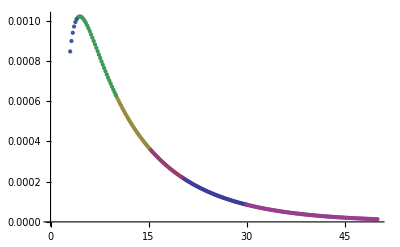

```mathematica
ListPlot[{t2l,t2l2,t2l3,t2l4,t2l5,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

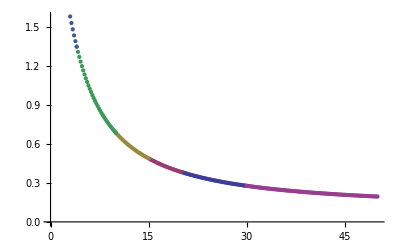

```mathematica
ListPlot[{t1l,t1l2,t1l3,t1l4,t1l5,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=2.0/R.dat",Join[t1l,t1l2,t1l3,t1l4,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=2.0/I.dat",Join[t2l,t2l2,t2l3,t2l4,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=2.0/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=2.0/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-M^2]
rm=M-Sqrt[M^2-M^2]
rmirror=40
```

1

1

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*M/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.3

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```